This script is a part of ANGEL project.
V 2.3.0
2018.02.10
(C) Vulpes Corsac

```mathematica
Clear["Global`*"];(* Variables clearing *)
```

```mathematica
importDir = "ImportData";(* Directory for importing data *)
exportDir = "ExportData";(* Directory for exporting main data *)
exportRoundDir = "RoundData";(* Subdirectory for exporting round data *)
exportRounds=True;
```

```mathematica
phaseColumnName="Theta"; (* Name of column in data file with phase *)
phaseSDColumnName="ThetaSD"; (* Name of column in data file with phase standart deviaton *)
frequencyColumnName="Fext";(* Name of column in data file with frequency *)
timeColumnName="Time";(* Name of column in data file with time *)
intervalColumnName="Interval";(* Name of column in data file with interval *)
roundColumnName="Round";(* Name of column in data file with round *)
```

```mathematica
Kprt={-1.,-1.,-1.};(* K^prt for all resonances *)
```

```mathematica
importDataMask="Continuous*.dat";(* Mask to search kinetics data files *)
```

```mathematica
fileNames = FileNames[importDataMask,FileNameJoin[{NotebookDirectory[],importDir}]];(* Getting all file names that matches template in import directory *)
filesAmmount=Length[fileNames];(* Ammount of kinetic files *)
```

```mathematica
DataNames=ParallelTable[Import[fileNames[[fileNumber]]][[1]],{fileNumber,filesAmmount}];(* Getting data headers *)
DataWithNoIntervalSelection=ParallelTable[Import[fileNames[[fileNumber]]][[2;;]],{fileNumber,filesAmmount}];(* Getting experimental data *)
DataOrigins={};(* File number and interval number will be here *)
DataRounds={};(* Rounds in a dataset will be here *)
```

```mathematica
Data=ParallelTable[0,{i,0}];(* Here actual data will be *)
For[fileNumber=1,fileNumber≤filesAmmount,fileNumber++,(* For all files *)
Intervals=DeleteDuplicates[DataWithNoIntervalSelection[[fileNumber,All,Position[DataNames[[fileNumber]],intervalColumnName][[1,1]]]]];(* Get all the intervals in the file *)
For[IntervalNumber=1,IntervalNumber≤Length[Intervals],IntervalNumber++,(* For all intervals *)
IntervalData=Select[DataWithNoIntervalSelection[[fileNumber]],#[[Position[DataNames[[fileNumber]],intervalColumnName][[1,1]]]]==Intervals[[IntervalNumber]]&];(* Get data for a single interval *)
AppendTo[DataOrigins,"File "<>ToString[fileNumber]<>" Interval "<>ToString[IntervalNumber]];(* Appending data origins *)
AppendTo[Data,IntervalData];(* Append interval data to actual data table *)
]
];
```

```mathematica
phaseTimeData=ParallelTable[Transpose[{(* Cutting dependency of phase from time just to show *)
Data[[fileNumber,All,Position[DataNames[[fileNumber]],timeColumnName][[1,1]]]],
Data[[fileNumber,All,Position[DataNames[[fileNumber]],phaseColumnName][[1,1]]]]
}],{fileNumber,filesAmmount}];
phaseSDTimeData=ParallelTable[Transpose[{(* Cutting dependency of phase standart deviation from time just to show *)
Data[[fileNumber,All,Position[DataNames[[fileNumber]],timeColumnName][[1,1]]]],
Data[[fileNumber,All,Position[DataNames[[fileNumber]],phaseSDColumnName][[1,1]]]]
}],{fileNumber,filesAmmount}];
```

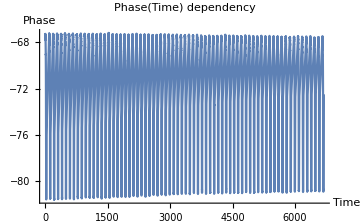
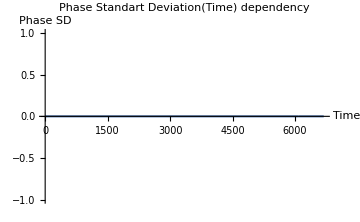

```mathematica
{ListPlot[phaseTimeData,PlotRange->All, Joined->True,ImageSize->Medium,AxesLabel->{"Time","Phase"},PlotLabel->"Phase(Time) dependency"],
ListPlot[phaseSDTimeData,PlotRange->All, Joined->True,ImageSize->Medium,AxesLabel->{"Time","Phase SD"},PlotLabel->"Phase Standart Deviation(Time) dependency"]}(* Plotting data from above *)
```

```mathematica
Temperature[i_,Fres_, F0_] := N[(Fres-F0)/Kprt[[i]]];(* Evaluating temperature for resonance i *)
paraboloid[y0_,A_,μ_,x_] := y0 + A(x-μ)^2;(* Parabola function *)
gaussian[y0_,A_,μ_, σ_, x_] := y0 + A/(σ Sqrt[Pi/2])×Exp[(-2(x-μ)^2)/σ^2];(* Gauss function *)
lorenz[y0_,A_,μ_, σ_, x_]:=y0 + (2A)/Pi×σ/(4 (x-μ)^2+σ^2);(* Lorenz function *)
linear[A_,B_,x_] := A x+B;(* linear function *)
```

```mathematica
fileNumber=1;
KineticsMinAll=Table[(* Calculationg fast but just searching for a phase min *)
Rounds=DeleteDuplicates[Data[[InvervalNumber,All,Position[DataNames[[fileNumber]],roundColumnName][[1,1]]]]];(* Getting all rounds *)
AppendTo[DataRounds,Length[Rounds]];(* Saving rounds ammount for every dataset *)
KineticsMin=Table[(* For every round *)
RoundData=Select[Data[[InvervalNumber]],#[[Position[DataNames[[fileNumber]],roundColumnName][[1,1]]]]==Rounds[[RoundNumber]]&];(* Getting round data *)
MinPhase=Min[RoundData[[All,Position[DataNames[[fileNumber]],phaseColumnName][[1,1]]]]];(* Getting phase minimum *)
MinPhasePosition=Position[RoundData[[All,Position[DataNames[[fileNumber]],phaseColumnName][[1,1]]]],MinPhase][[1,1]];(* Getting position *)
ResonanceFrequency=RoundData[[All,Position[DataNames[[fileNumber]],frequencyColumnName][[1,1]]]][[MinPhasePosition]];(* Getting frequency *)
ResonanceTime=RoundData[[All,Position[DataNames[[fileNumber]],timeColumnName][[1,1]]]][[MinPhasePosition]];(* Getting time *)
{ResonanceTime,ResonanceFrequency}(* Exporting calculated point *)
,{RoundNumber,DataRounds[[InvervalNumber]]-1}(* Last round can be not full, let's ignore it *)
];
KineticsMin[[All,2]]=Temperature[InvervalNumber,KineticsMin[[All,2]],KineticsMin[[1,2]]];(* Calculating temperature from frequency *)
KineticsMin(* Exporting calculated kinetics *)
,{InvervalNumber,Length[Data]}];
```

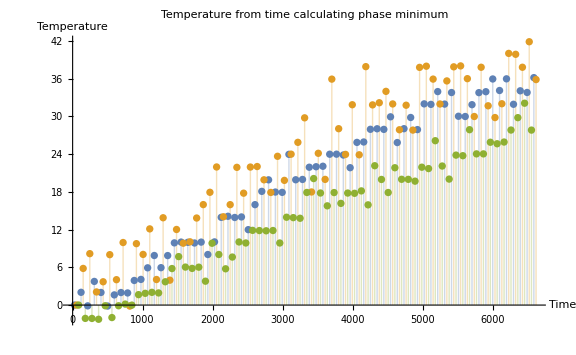

```mathematica
MinKineticsPlt=ListPlot[KineticsMinAll,PlotRange->All, Joined->False,ImageSize->Large,Filling->Axis,
AxesLabel->{"Time","Temperature"},PlotLabel->"Temperature from time calculating phase minimum"](* Plotting kinetics min without fitting *)
```

```mathematica
For[i=1,i≤Length[KineticsMinAll],i++,PrependTo[KineticsMinAll[[i]],{DataOrigins[[i]]<>" Time",DataOrigins[[i]]<>" Temperature"}]](* Adding headers for columns *)
KineticsMinAll = ParallelTable[Transpose[KineticsMinAll[[i]]],{i,1,Length[KineticsMinAll]}];(* Transposing for joining *)
tmp=KineticsMinAll[[1]];(* Join starting point *)
For[i=2,i≤Length[KineticsMinAll],i++,tmp=tmp~Join~KineticsMinAll[[i]]];(* Joining *)
KineticsMinAll=tmp;(* Saving joined result *)
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],exportDir,"KineticsMinAll.png"}],MinKineticsPlt];(* Exporting plot *)
Export[FileNameJoin[{NotebookDirectory[],exportDir,"KineticsMinAll.xlsx"}],KineticsMinAll];(* Exporting calculated data *)
KineticsMinAll=Transpose[Import[FileNameJoin[{NotebookDirectory[],exportDir,"KineticsMinAll.xlsx"}]][[1]]];
Export[FileNameJoin[{NotebookDirectory[],exportDir,"KineticsMinAll.xlsx"}],KineticsMinAll];(* Exporting calculated data in a normal format *)
```

```mathematica
fileNumber=1;
KineticsFitAll=Table[
KineticsFit=Table[
RoundDataRaw=Select[Data[[IntervalNumber]],#[[Position[DataNames[[fileNumber]],roundColumnName][[1,1]]]]==Rounds[[RoundNumber]]&];(* Getting row round data *)
RoundData=Transpose[{(* Getting Phase(Frequency) dependency *)
RoundDataRaw[[All,Position[DataNames[[fileNumber]],frequencyColumnName][[1,1]]]],
RoundDataRaw[[All,Position[DataNames[[fileNumber]],phaseColumnName][[1,1]]]]
}];
PhaseMin=Min[RoundData[[All,2]]];(* Getting phase minimum *)
If[Length[PhaseMin]>0,PhaseMin=PhaseMin[[1]]];(* Just in case *)
PhaseMax=Max[RoundData[[All,2]]];(* Getting phase maximum *)
If[Length[PhaseMax]>0,PhaseMax=PhaseMax[[1]]];(* Just in case *)
σ0 = Length[Select[RoundData,PhaseMin≤#[[2]]≤PhaseMin+(PhaseMax-PhaseMin)/2&]];(* For first approximation *)
(* Parabolic fit *)
ParabolicPart = 0.25;(* Part from Min to Max-Min *)
RoundDataParaboloid =Select[RoundData,(PhaseMin≤#[[2]]≤PhaseMin+(PhaseMax-PhaseMin)×ParabolicPart)&] ;
nlmRoundParaboloid = NonlinearModelFit[
RoundDataParaboloid,paraboloid[y0,A,μ,t],
{{y0,Max[RoundDataParaboloid[[All,2]]]},
{A,RoundDataParaboloid[[Ordering[RoundDataParaboloid[[All, 2]],1], 2]][[1]]},
{μ,RoundDataParaboloid[[Ordering[RoundDataParaboloid[[All, 2]],1], 1]][[1]]}},
t];
parametersTableRoundParaboloid = nlmRoundParaboloid["ParameterTable"];
FresParaboloid = parametersTableRoundParaboloid[[1,1,4,2]];
δFresParaboloid=100×Abs[parametersTableRoundParaboloid[[1,1,4,3]]/parametersTableRoundParaboloid[[1,1,4,2]]];
FfirstParaboloid = Switch[RoundNumber==1,True,FresParaboloid,False, FfirstParaboloid];
TempParaboloid = Temperature[IntervalNumber,FresParaboloid,FfirstParaboloid];
If[exportRounds,
RoundPlt =Show[{ListPlot[RoundData],Plot[paraboloid[parametersTableRoundParaboloid [[1,1,2,2]],parametersTableRoundParaboloid [[1,1,3,2]],parametersTableRoundParaboloid [[1,1,4,2]],t],{t,RoundDataParaboloid[[1,1]],RoundDataParaboloid[[-1,1]]},PlotRange->All,ImageSize->Large,ColorFunction->Function[{x,y},Red]]}];Export[FileNameJoin[{NotebookDirectory[],exportRoundDir,"File "<>ToString[fileNumber]<>", Interval "<>ToString[IntervalNumber]<>", Round "<>ToString[RoundNumber]<>".png"}],RoundPlt];
,False];(* Exporting plot for every round *)
FrequencyTimeData=Transpose[{(* Getting Time(Frequency) dependency *)
RoundDataRaw[[All,Position[DataNames[[fileNumber]],frequencyColumnName][[1,1]]]],
RoundDataRaw[[All,Position[DataNames[[fileNumber]],timeColumnName][[1,1]]]]
}];
nlmFrequencyTime= NonlinearModelFit[FrequencyTimeData,linear[A,B,x],{{A,1},{B,1}},x];
parametersTableFrequencyTime= nlmFrequencyTime["ParameterTable"];
TimeParaboloid = linear[parametersTableFrequencyTime[[1,1,2,2]],parametersTableFrequencyTime[[1,1,3,2]],FresParaboloid];
{TimeParaboloid,TempParaboloid}
,{RoundNumber,DataRounds[[IntervalNumber]]-1}];
KineticsFit
,{IntervalNumber,Length[Data]}];
```

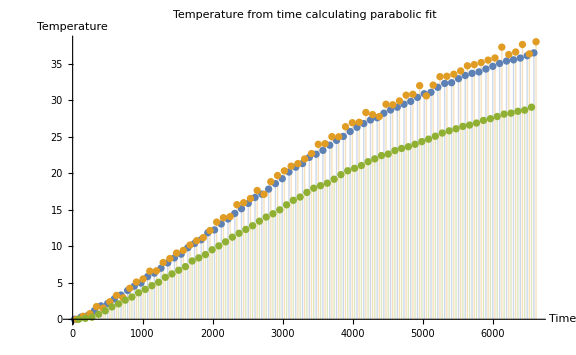

```mathematica
FitKineticsPlt=ListPlot[KineticsFitAll,PlotRange->All, Joined->False,ImageSize->Large,Filling->Axis,
AxesLabel->{"Time","Temperature"},PlotLabel->"Temperature from time calculating parabolic fit"](* Plotting kinetics min with parabolic fit *)
```

```mathematica
For[i=1,i≤Length[KineticsFitAll],i++,PrependTo[KineticsFitAll[[i]],{DataOrigins[[i]]<>" Time",DataOrigins[[i]]<>" Temperature"}]](* Adding headers for columns *)
KineticsFitAll = ParallelTable[Transpose[KineticsFitAll[[i]]],{i,1,Length[KineticsFitAll]}];(* Transposing for joining *)
tmp=KineticsFitAll[[1]];(* Join starting point *)
For[i=2,i≤Length[KineticsFitAll],i++,tmp=tmp~Join~KineticsFitAll[[i]]];(* Joining *)
KineticsFitAll=tmp;(* Saving joined result *)
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],exportDir,"KineticsFitAll.png"}],FitKineticsPlt];(* Exporting plot *)
Export[FileNameJoin[{NotebookDirectory[],exportDir,"KineticsFitAll.xlsx"}],KineticsFitAll];(* Exporting calculated data *)
KineticsFitAll=Transpose[Import[FileNameJoin[{NotebookDirectory[],exportDir,"KineticsFitAll.xlsx"}]][[1]]];
Export[FileNameJoin[{NotebookDirectory[],exportDir,"KineticsFitAll.xlsx"}],KineticsFitAll];(* Exporting calculated data in a normal format *)
```